```mathematica
SetDirectory["/home/ethan/spring20/comphys/week3/rooney/"]
```

/home/ethan/spring20/comphys/week3/rooney

```mathematica
res[n_, i_] := ReadList[ "!./integral2 1.3, 6.28318530717958647692528676655900576901, 0, " <>ToString[n]<> ", " <>ToString[i] <> " ", {Number, Number, Number, Number, Number, Number, Number, Number, Number}]
```

```mathematica
data = res[0.01, 2.526];
```

```mathematica
ListPlot[{ data[[All,{1,8}]],
		data[[All,{1,9}]],
		data[[All,{1,6}]]},
		Joined->True, Frame->True, FrameLabel->{"t","Energy"}, PlotRange->All]
```

-Graphics-

```mathematica
res[n_, i_] := ReadList[ "!./pb 1.0001, 6.28318430717958647692528676655900576901, 0, " <>ToString[n]<> ", " <>ToString[i] <> " ", {Number, Number, Number, Number, Number, Number, Number, Number, Number}]
(*data = res[0.0001, 20];*)
ListPlot[{ data[[All,{4,5}]](*,
		data[[All,{1,3}]],
		data[[All, {1,4}]],
		data[[All, {1,5}]](*,
		data[[All, {1,6}]]*)*)},
		PlotLegends->{"v_x", "v_y", "x", "y", "Energy", "r"},
		Joined->True, Frame->True, FrameLabel->{"x (AU)","y (AU)"}, PlotLabel->Text[Style["1/r^3 Universe",FontSize->18]]]
Min[data[[All, 4]]]
```

-Graphics-

-1.91527

```mathematica
data = Table[{n,N[(Extract[ReadList[ "!./integral2 1, 6.28318530717958647692528676655900576901, 0, " <>ToString[n]<> ", 0.5 | tail -n 1", {Number, Number, Number, Number, Number, Number, Number}][[1]],{6}]+(2*Pi*Pi))/(2*Pi*Pi),20]},{n,{0.1, 0.03, 0.01, 0.003, 0.001, 0.0003, 0.0001}}]
```

{{0.1,0.0176536},{0.03,0.00173948},{0.01,0.0000873084},{0.003,2.56072×10^-6},{0.001,9.65174×10^-8},{0.0003,2.62344×10^-9},{0.0001,9.73231×10^-11}}

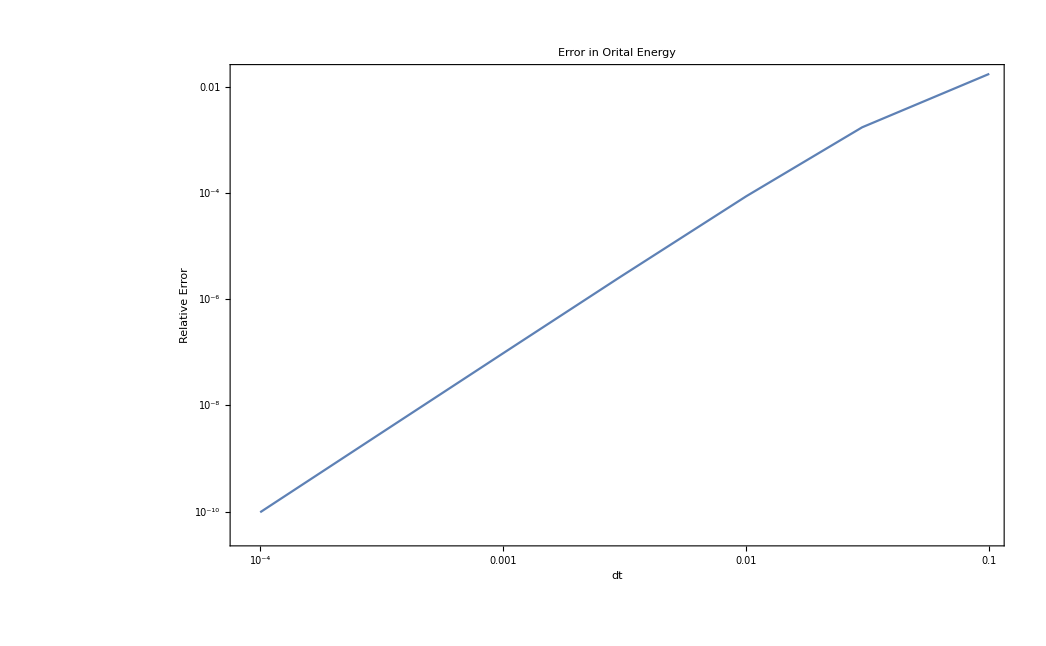

```mathematica
ListLogLogPlot[data, Joined->True, Frame->True, FrameLabel->{"dt", "Relative Error"}, PlotLabel->Text[Style["Error in Orital Energy",FontSize->18]]]
```

```mathematica
(Log[data[[3,2]]]-Log[data[[5,2]]])/(Log[data[[3,1]]]-Log[data[[5,1]]])
```

2.95645